```mathematica
β[ω_,δ_,t_,ϵ_]:=
β[ω,δ,t,ϵ]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[14],Join[Table[{i,i-1},{i,Range[2,14,1]}],Table[{i,i+1},{i,Range[1,14,1]}],Table[{2n-1,14-2n+2},{n,4}],Table[{14-2n+2,2n-1},{n,3}]]->-t]
```

```mathematica
T1[t_]:=T1[t]=ReplacePart[0*IdentityMatrix[14],Table[{2n,14-2n+1},{n,3}]->t]
```

```mathematica
TT[t_]:=ReplacePart[0*IdentityMatrix[14],Table[{2n,2n},{n,3}]->t]
```

```mathematica
Clear[LEFT]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=
Module[{J=Inverse[β[ω,0.0001,1,0]],
B:=Inverse[β[ω,0.0001,1,0]],T1:=T1[1]},
Do[J=Inverse[IdentityMatrix[14]-B.ConjugateTranspose[T1].J.T1].B,10000];
 J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=SR[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=SL[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SL[ω,δ,t,ϵ].TT[t].SR[ω,δ,t,ϵ].TT[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SR[ω,δ,t,ϵ].TT[t].SL[ω,δ,t,ϵ].TT[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].TT[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Abs[Tr[gdd[ω,δ,t,ϵ].TT[t].grr[ω,δ,t,ϵ].TT[t]-TT[t].GNON[ω,δ,t,ϵ].TT[t].GNON[ω,δ,t,ϵ]]]
```

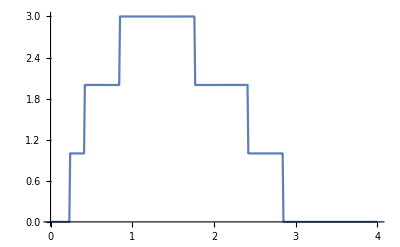

```mathematica
ListLinePlot[Table[{ω,tr[ω,0.0001,1,0]},{ω,Range[0,4,0.01]}]]
```

```mathematica
Pri[ω_]:=tr[ω,0.0001,1,0]
```

```mathematica
k14:=k14=Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/14imp100.csv"]
k28:=k28=Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/28imp100.csv"]
k42:=k42=Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/42imp100.csv"]
k56:=k56=Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/56imp100.csv"]
k70:=k70=Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/70imp100.csv"]
k84:=k84=Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/84imp100.csv"]
k100:=k100=Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/100imp100.csv"]
k114:=k114=Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/114imp100.csv"]
k126:=k126=Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/126imp100.csv"]
```

```mathematica
f[ω_]:={Pri[ω],k14[[ω*100+1]][[2]],k28[[ω*100+1]][[2]],k42[[ω*100+1]][[2]],k56[[ω*100+1]][[2]],k70[[ω*100+1]][[2]],k84[[ω*100+1]][[2]],k100[[ω*100+1]][[2]],k114[[ω*100+1]][[2]],k126[[ω*100+1]][[2]]}
```

```mathematica
ββ[ω_,j_,x_]:=Table[-f[ω][[i+1]]+f[ω][[i]],{i,j,x}]
```

```mathematica
γ[ω_,n1_]:=f[ω][[n1+1]]+f[ω][[n1-1]]-2f[ω][[n1]]
```

```mathematica
γ[1,5]
```

0.0558386

```mathematica
RandomSample[Join[RandomChoice[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14},100],Table[imp,0]],100]
```

{imp10,imp2,imp3,imp13,imp5,imp7,imp1,imp14,imp11,imp1,imp2,imp8,imp7,imp12,imp8,imp5,imp1,imp5,imp7,imp8,imp6,imp10,imp12,imp3,imp4,imp9,imp14,imp12,imp13,imp1,imp6,imp1,imp11,imp9,imp10,imp14,imp10,imp3,imp11,imp1,imp3,imp12,imp9,imp9,imp4,imp10,imp14,imp7,imp3,imp14,imp3,imp6,imp2,imp3,imp5,imp8,imp12,imp12,imp5,imp10,imp5,imp1,imp10,imp2,imp5,imp14,imp2,imp3,imp11,imp13,imp6,imp10,imp2,imp3,imp2,imp10,imp10,imp12,imp9,imp3,imp1,imp7,imp1,imp12,imp8,imp3,imp5,imp13,imp2,imp14,imp14,imp1,imp12,imp10,imp13,imp12,imp9,imp4,imp5,imp8}

```mathematica
Clear[imp1,imp2,imp3,imp4]
```

```mathematica
imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=Inverse[Module[{κ=β[ω,0.0001,1,0],μ=RandomInteger[{1,14}]},ReplacePart[κ,{{μ,μ}}->ω+ⅈ*0.0001-ϵ1]]]
```

```mathematica
imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=Inverse[Module[{κ=β[ω,0.0001,1,0],μ1=RandomInteger[{1,7}],μ2=RandomInteger[{8,14}]},ReplacePart[κ,{{μ2,μ2},{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]]
```

```mathematica
imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=Inverse[Module[{κ=β[ω,0.0001,1,0],μ1=RandomInteger[{1,7}],μ2=RandomInteger[{8,14}]},ReplacePart[κ,{{μ2,μ2},{μ1,μ1}}->ω+ⅈ*0.0001]]]
```

```mathematica
deltae[ϵ1_]:=Module[{Tin=T1[1],T=TT[1]},
tra:=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{1,1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{2,2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{3,3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{4,4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{5,5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{6,6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{7,7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{8,8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{9,9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{10,10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{11,11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{12,12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{13,13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp10,imp2,imp3,imp13,imp5,imp7,imp1,imp14,imp11,imp1,imp2,imp8,imp7,imp12,imp8,imp5,imp1,imp5,imp7,imp8,imp6,imp10,imp12,imp3,imp4,imp9,imp14,imp12,imp13,imp1,imp6,imp1,imp11,imp9,imp10,imp14,imp10,imp3,imp11,imp1,imp3,imp12,imp9,imp9,imp4,imp10,imp14,imp7,imp3,imp14,imp3,imp6,imp2,imp3,imp5,imp8,imp12,imp12,imp5,imp10,imp5,imp1,imp10,imp2,imp5,imp14,imp2,imp3,imp11,imp13,imp6,imp10,imp2,imp3,imp2,imp10,imp10,imp12,imp9,imp3,imp1,imp7,imp1,imp12,imp8,imp3,imp5,imp13,imp2,imp14,imp14,imp1,imp12,imp10,imp13,imp12,imp9,imp4,imp5,imp8}]};b=Module[{},
(*Print[Dimensions[list]];*)sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}]; J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]];
b];Table[{ω,tra},{ω,Range[0,4,0.01]}]]
```

```mathematica
Table[deltae[0.5],100]
```

{{{0.,1.93804×10^-7},{0.01,0.0000114901},{0.02,0.0000144786},{0.03,1.52663×10^-6},{0.04,0.0000123634},{0.05,0.0000208244},{0.06,0.000116527},{0.07,0.000141255},{0.08,5.78072×10^-6},{0.09,0.000211626},382,{3.92,9.11563×10^-8},{3.93,1.81335×10^-9},{3.94,2.6829×10^-8},{3.95,1.55689×10^-9},{3.96,1.5344×10^-9},{3.97,1.51204×10^-9},{3.98,1.48055×10^-9},{3.99,1.62104×10^-9},{4.,1.93974×10^-8}},98,{1}}
 |  |  |  |

```mathematica
intg[lim1_,lim2_,λ_]:=NIntegrate[Interpolation[Table[{ω,Mean[ββ[ω,1,7]]*(tr[ω,0.0001,1,0]-%117[[λ]][[ω*100+1]][[2]])},{ω,Range[lim1,lim2,0.01]}]][ω],{ω,lim1,lim2}]/NIntegrate[Interpolation[Table[{ω,(Mean[ββ[ω,1,7]]*Mean[ββ[ω,1,7]])},{ω,Range[lim1,lim2,0.01]}]][ω],{ω,lim1,lim2}]
```

```mathematica
intg[0.9,1.5,4]
```

6.9192

```mathematica
{Table[7,100],%132}
```

{{7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7},{7.07825,6.53935,6.96204,6.9192,6.94095,6.86543,7.16141,7.07584,7.13687,6.97366,7.08807,6.7787,7.06651,6.84439,7.06638,6.83839,6.96583,6.80481,6.82808,6.6912,6.84719,6.92799,7.08603,6.89628,6.85138,7.00275,6.76583,6.87358,6.87174,7.01025,6.70537,6.66912,6.68407,7.04182,6.78948,6.70495,6.93661,6.87074,6.82533,6.86065,7.04607,6.88926,6.9463,6.89649,7.15753,6.85779,6.9414,6.97977,7.05469,6.90211,6.97505,6.92337,6.80402,6.70226,6.68162,6.82139,6.94494,7.08026,6.93596,6.73716,6.87172,6.9621,7.0217,7.06202,6.76706,7.09574,6.8174,6.91751,6.68467,6.8943,6.8818,6.84923,6.89223,6.8889,6.80086,6.88824,6.91253,6.93599,6.88153,6.95782,6.78144,6.99948,6.96187,7.03604,7.03201,7.02904,6.88119,6.91166,6.62052,6.94546,6.8803,6.82518,6.8892,6.85434,6.81006,6.76543,7.06088,6.8513,7.13813,7.04847}}

```mathematica
Transpose[%145]
```

{{7,7.07825},{7,6.53935},{7,6.96204},{7,6.9192},{7,6.94095},{7,6.86543},{7,7.16141},{7,7.07584},{7,7.13687},{7,6.97366},{7,7.08807},{7,6.7787},{7,7.06651},{7,6.84439},{7,7.06638},{7,6.83839},{7,6.96583},{7,6.80481},{7,6.82808},{7,6.6912},{7,6.84719},{7,6.92799},{7,7.08603},{7,6.89628},{7,6.85138},{7,7.00275},{7,6.76583},{7,6.87358},{7,6.87174},{7,7.01025},{7,6.70537},{7,6.66912},{7,6.68407},{7,7.04182},{7,6.78948},{7,6.70495},{7,6.93661},{7,6.87074},{7,6.82533},{7,6.86065},{7,7.04607},{7,6.88926},{7,6.9463},{7,6.89649},{7,7.15753},{7,6.85779},{7,6.9414},{7,6.97977},{7,7.05469},{7,6.90211},{7,6.97505},{7,6.92337},{7,6.80402},{7,6.70226},{7,6.68162},{7,6.82139},{7,6.94494},{7,7.08026},{7,6.93596},{7,6.73716},{7,6.87172},{7,6.9621},{7,7.0217},{7,7.06202},{7,6.76706},{7,7.09574},{7,6.8174},{7,6.91751},{7,6.68467},{7,6.8943},{7,6.8818},{7,6.84923},{7,6.89223},{7,6.8889},{7,6.80086},{7,6.88824},{7,6.91253},{7,6.93599},{7,6.88153},{7,6.95782},{7,6.78144},{7,6.99948},{7,6.96187},{7,7.03604},{7,7.03201},{7,7.02904},{7,6.88119},{7,6.91166},{7,6.62052},{7,6.94546},{7,6.8803},{7,6.82518},{7,6.8892},{7,6.85434},{7,6.81006},{7,6.76543},{7,7.06088},{7,6.8513},{7,7.13813},{7,7.04847}}

```mathematica
Join[Transpose[{Table[7,100],%132}],Transpose[{Table[6,100],%131}],Transpose[{Table[5,100],%114}],Transpose[{Table[4,100],%73}],Transpose[{Table[3,100],%90}],Transpose[{Table[2,100],%98}],Transpose[{Table[1,100],%106}]]
```

{{7,7.07825},{7,6.53935},{7,6.96204},{7,6.9192},{7,6.94095},{7,6.86543},{7,7.16141},{7,7.07584},{7,7.13687},{7,6.97366},{7,7.08807},{7,6.7787},{7,7.06651},{7,6.84439},{7,7.06638},{7,6.83839},{7,6.96583},{7,6.80481},{7,6.82808},{7,6.6912},{7,6.84719},{7,6.92799},{7,7.08603},{7,6.89628},{7,6.85138},{7,7.00275},{7,6.76583},{7,6.87358},{7,6.87174},{7,7.01025},{7,6.70537},{7,6.66912},{7,6.68407},{7,7.04182},{7,6.78948},{7,6.70495},{7,6.93661},{7,6.87074},{7,6.82533},{7,6.86065},{7,7.04607},{7,6.88926},{7,6.9463},{7,6.89649},{7,7.15753},{7,6.85779},{7,6.9414},{7,6.97977},{7,7.05469},{7,6.90211},{7,6.97505},{7,6.92337},{7,6.80402},{7,6.70226},{7,6.68162},{7,6.82139},{7,6.94494},{7,7.08026},{7,6.93596},{7,6.73716},{7,6.87172},{7,6.9621},{7,7.0217},{7,7.06202},{7,6.76706},{7,7.09574},{7,6.8174},{7,6.91751},{7,6.68467},{7,6.8943},{7,6.8818},{7,6.84923},{7,6.89223},{7,6.8889},{7,6.80086},{7,6.88824},{7,6.91253},{7,6.93599},{7,6.88153},{7,6.95782},{7,6.78144},{7,6.99948},{7,6.96187},{7,7.03604},{7,7.03201},{7,7.02904},{7,6.88119},{7,6.91166},{7,6.62052},{7,6.94546},{7,6.8803},{7,6.82518},{7,6.8892},{7,6.85434},{7,6.81006},{7,6.76543},{7,7.06088},{7,6.8513},{7,7.13813},{7,7.04847},{6,6.12555},{6,6.26514},{6,5.92818},{6,6.03313},{6,5.95201},{6,6.03502},{6,6.06434},{6,5.82361},{6,6.23969},{6,6.10335},{6,6.07553},{6,6.03243},{6,6.16288},{6,6.06536},{6,5.99633},{6,6.00033},{6,6.11281},{6,6.02479},{6,6.00611},{6,5.85925},{6,5.8461},{6,5.88507},{6,6.01672},{6,5.84072},{6,6.01959},{6,6.00502},{6,6.11205},{6,6.01062},{6,6.06377},{6,5.95565},{6,6.09998},{6,6.29698},{6,5.83896},{6,6.03958},{6,6.03951},{6,5.94342},{6,5.9727},{6,6.01477},{6,5.91905},{6,5.9769},{6,5.998},{6,5.98179},{6,5.75244},{6,5.88456},{6,6.02668},{6,5.95983},{6,6.01148},{6,5.94988},{6,6.09948},{6,5.88714},{6,6.01575},{6,5.92145},{6,5.92397},{6,5.93783},{6,5.97937},{6,5.99439},{6,6.13902},{6,5.95961},{6,6.08194},{6,6.00151},{6,5.84119},{6,6.07206},{6,6.03414},{6,5.91467},{6,6.1563},{6,6.06842},{6,6.07152},{6,5.89674},{6,6.08445},{6,6.00792},{6,5.78854},{6,5.92672},{6,6.0432},{6,6.07062},{6,5.97701},{6,5.92096},{6,5.91498},{6,5.95779},{6,5.91103},{6,5.84623},{6,6.14261},{6,5.97987},{6,6.08964},{6,6.10847},{6,5.99127},{6,5.98823},{6,5.83923},{6,6.14637},{6,6.08906},{6,5.9393},{6,6.13106},{6,6.03914},{6,6.23913},{6,5.9436},{6,6.2493},{6,6.00122},{6,6.17588},{6,6.02124},{6,6.08132},{6,6.0237},{5,5.0021},{5,5.01626},{5,4.93655},{5,5.20099},{5,5.08139},{5,5.01603},{5,4.98659},{5,5.05049},{5,4.99174},{5,5.07249},{5,4.85145},{5,5.06829},{5,4.9275},{5,5.1645},{5,5.01197},{5,4.96105},{5,5.08534},{5,5.12923},{5,5.06089},{5,5.11108},{5,4.96735},{5,4.9015},{5,5.0411},{5,4.87599},{5,5.02622},{5,4.94936},{5,5.01957},{5,5.00002},{5,5.05533},{5,4.92985},{5,5.02522},{5,5.04209},{5,5.11067},{5,4.83263},{5,5.113},{5,5.0236},{5,4.83719},{5,4.87919},{5,4.89421},{5,5.12463},{5,4.95932},{5,4.98548},{5,5.09982},{5,5.10091},{5,4.89221},{5,4.99286},{5,5.04412},{5,5.16865},{5,4.88392},{5,5.04867},{5,4.90787},{5,5.09726},{5,4.93135},{5,5.03181},{5,4.99989},{5,4.90943},{5,5.06304},{5,5.05079},{5,5.09269},{5,4.86077},{5,4.90179},{5,4.97286},{5,5.03661},{5,5.05332},{5,4.99499},{5,5.09267},{5,5.04909},{5,5.02978},{5,4.92514},{5,4.89659},{5,5.02373},{5,4.9569},{5,4.90991},{5,4.98744},{5,4.85339},{5,4.90825},{5,5.01758},{5,4.84705},{5,4.84339},{5,4.93228},{5,5.12057},{5,4.97127},{5,5.01594},{5,5.0459},{5,4.91348},{5,5.02531},{5,5.03987},{5,5.04276},{5,4.85334},{5,5.08209},{5,4.95416},{5,4.83027},{5,5.0441},{5,5.05998},{5,5.10827},{5,4.88276},{5,5.04878},{5,5.11623},{5,5.16933},{5,5.0483},{4,3.96046},{4,4.05121},{4,4.06398},{4,4.07735},{4,4.00293},{4,4.03482},{4,4.03079},{4,4.04097},{4,4.0515},{4,4.00354},{4,4.04823},{4,4.12955},{4,4.01643},{4,3.9694},{4,4.04203},{4,4.08465},{4,3.87083},{4,3.9951},{4,4.14747},{4,3.80406},{4,3.83047},{4,3.97832},{4,3.96793},{4,4.03391},{4,3.97503},{4,3.98171},{4,3.93055},{4,4.05283},{4,3.97479},{4,4.04042},{4,4.05168},{4,4.06719},{4,3.9528},{4,4.03631},{4,4.08743},{4,4.03893},{4,4.0368},{4,4.05152},{4,3.99295},{4,4.01062},{4,4.17398},{4,3.94894},{4,4.15825},{4,4.13491},{4,4.12195},{4,4.19223},{4,4.13186},{4,4.18117},{4,4.08239},{4,3.9083},{4,3.85719},{4,4.16023},{4,4.17176},{4,3.98384},{4,4.07989},{4,3.97916},{4,4.06169},{4,3.86116},{4,3.97072},{4,3.98109},{4,3.99632},{4,3.98357},{4,4.13387},{4,3.89647},{4,3.93642},{4,4.01733},{4,4.07253},{4,4.02913},{4,4.14589},{4,4.05524},{4,3.89299},{4,3.72452},{4,3.91267},{4,3.9499},{4,4.07102},{4,3.97801},{4,4.07009},{4,3.87028},{4,3.99908},{4,4.05554},{4,3.90514},{4,4.13162},{4,4.30785},{4,4.14341},{4,4.0425},{4,3.869},{4,4.00175},{4,3.70974},{4,3.91751},{4,4.05741},{4,4.05609},{4,3.91696},{4,3.95449},{4,4.02505},{4,4.06867},{4,3.95103},{4,4.1296},{4,4.08146},{4,4.0759},{4,3.90943},{3,3.04423},{3,3.14959},{3,2.95542},{3,3.10666},{3,3.0278},{3,3.03809},{3,2.97196},{3,3.05313},{3,3.15865},{3,3.21791},{3,3.01449},{3,2.95109},{3,3.14227},{3,3.14412},{3,3.1048},{3,2.94087},{3,2.89005},{3,3.0691},{3,2.98228},{3,3.20103},{3,3.12031},{3,2.98528},{3,2.93075},{3,3.10186},{3,3.05051},{3,3.05555},{3,3.02155},{3,3.06346},{3,2.94263},{3,3.05488},{3,3.09406},{3,2.95815},{3,3.04967},{3,2.96873},{3,3.0136},{3,3.08522},{3,3.08052},{3,3.12784},{3,3.10075},{3,2.99206},{3,3.11349},{3,2.97853},{3,3.08947},{3,3.04191},{3,3.18155},{3,3.07082},{3,2.984},{3,3.03196},{3,2.96752},{3,3.05302},{3,3.05646},{3,3.09017},{3,2.9639},{3,3.09814},{3,3.03122},{3,3.06235},{3,2.99208},{3,3.137},{3,3.01242},{3,3.12253},{3,3.10671},{3,3.04702},{3,3.08647},{3,2.82565},{3,3.00847},{3,3.05972},{3,3.03164},{3,3.02434},{3,3.14492},{3,3.05555},{3,3.09658},{3,3.18072},{3,3.08129},{3,3.06064},{3,3.08213},{3,3.04818},{3,3.04753},{3,3.0264},{3,3.08969},{3,3.05581},{3,2.9813},{3,2.98181},{3,3.04182},{3,3.127},{3,3.06083},{3,3.02537},{3,3.02452},{3,2.98483},{3,3.05962},{3,2.94756},{3,3.01692},{3,2.9975},{3,3.00659},{3,3.07004},{3,3.17638},{3,3.04728},{3,3.14405},{3,3.04269},{3,3.03479},{3,3.12656},{2,1.91786},{2,1.945},{2,1.9753},{2,1.94026},{2,1.95569},{2,1.87674},{2,1.89217},{2,2.04061},{2,1.97471},{2,2.00934},{2,2.0144},{2,1.95077},{2,2.00647},{2,1.85485},{2,1.98537},{2,2.01399},{2,1.92437},{2,1.92887},{2,1.99507},{2,1.93182},{2,2.0024},{2,1.98542},{2,1.89845},{2,1.88492},{2,1.94962},{2,1.8959},{2,1.92772},{2,1.92441},{2,2.0252},{2,1.91056},{2,1.95368},{2,2.03782},{2,2.03269},{2,1.97588},{2,1.99555},{2,2.00605},{2,1.86606},{2,1.98827},{2,2.0487},{2,1.95363},{2,2.05505},{2,1.96992},{2,1.9417},{2,1.8977},{2,2.05215},{2,1.93165},{2,1.99851},{2,1.92479},{2,1.94199},{2,1.91314},{2,1.99098},{2,1.94893},{2,1.87743},{2,1.93758},{2,1.98093},{2,1.93824},{2,1.96353},{2,1.8899},{2,2.03769},{2,1.99574},{2,1.91326},{2,1.98945},{2,2.0539},{2,1.91489},{2,1.96762},{2,1.88467},{2,2.02165},{2,2.02654},{2,1.93191},{2,1.97672},{2,2.00814},{2,1.97109},{2,2.04632},{2,2.00414},{2,1.93579},{2,1.87377},{2,1.96266},{2,1.90823},{2,1.95305},{2,1.90565},{2,1.90127},{2,1.89436},{2,1.95108},{2,1.93951},{2,1.95672},{2,1.93546},{2,1.96906},{2,2.06482},{2,1.93803},{2,2.02446},{2,1.90023},{2,1.96019},{2,1.79173},{2,1.974},{2,1.90217},{2,1.93946},{2,2.01387},{2,1.94113},{2,1.9919},{2,1.92748},{1,0.950351},{1,1.01597},{1,0.934718},{1,0.991504},{1,0.960947},{1,1.02427},{1,0.942185},{1,1.02371},{1,0.981148},{1,0.988685},{1,0.991282},{1,0.98086},{1,0.996144},{1,1.05487},{1,0.94577},{1,1.00203},{1,1.00848},{1,0.95668},{1,0.946802},{1,0.962424},{1,0.950591},{1,1.04384},{1,0.994494},{1,1.00076},{1,0.927544},{1,1.01426},{1,0.99654},{1,0.960233},{1,0.974079},{1,0.96235},{1,0.925196},{1,1.00342},{1,1.04943},{1,0.997243},{1,0.943337},{1,0.970586},{1,0.948313},{1,0.974474},{1,0.986183},{1,0.903073},{1,1.02857},{1,0.996471},{1,0.983773},{1,0.987539},{1,0.975996},{1,0.945262},{1,0.952492},{1,1.0466},{1,0.987967},{1,0.982405},{1,1.01427},{1,0.974758},{1,0.998835},{1,0.943763},{1,1.03395},{1,1.01083},{1,1.01167},{1,0.987699},{1,0.941445},{1,1.00224},{1,1.01025},{1,0.999885},{1,0.979226},{1,0.942426},{1,1.01637},{1,0.97196},{1,0.96164},{1,0.989155},{1,0.975583},{1,0.993192},{1,0.989128},{1,0.974007},{1,1.01145},{1,1.00132},{1,1.00237},{1,1.05696},{1,0.97694},{1,0.993771},{1,0.928883},{1,1.02622},{1,1.00643},{1,0.98988},{1,0.984498},{1,1.02567},{1,0.994262},{1,0.996802},{1,0.97952},{1,0.949644},{1,0.951387},{1,0.983626},{1,0.979198},{1,0.902628},{1,0.979749},{1,0.987082},{1,0.988437},{1,1.02989},{1,1.03678},{1,1.02476},{1,0.937575},{1,1.01661}}

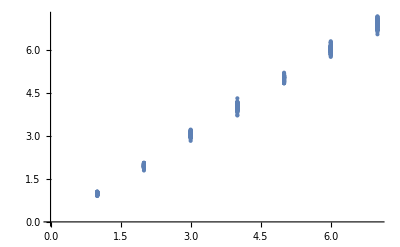

```mathematica
ListPlot[%149]
```

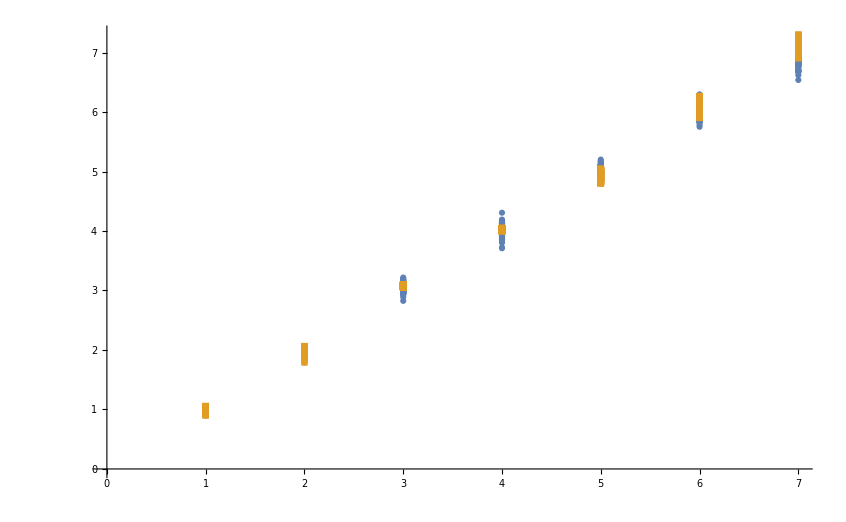

```mathematica
ListPlot[{%149,%153},PlotMarkers->Automatic]
```

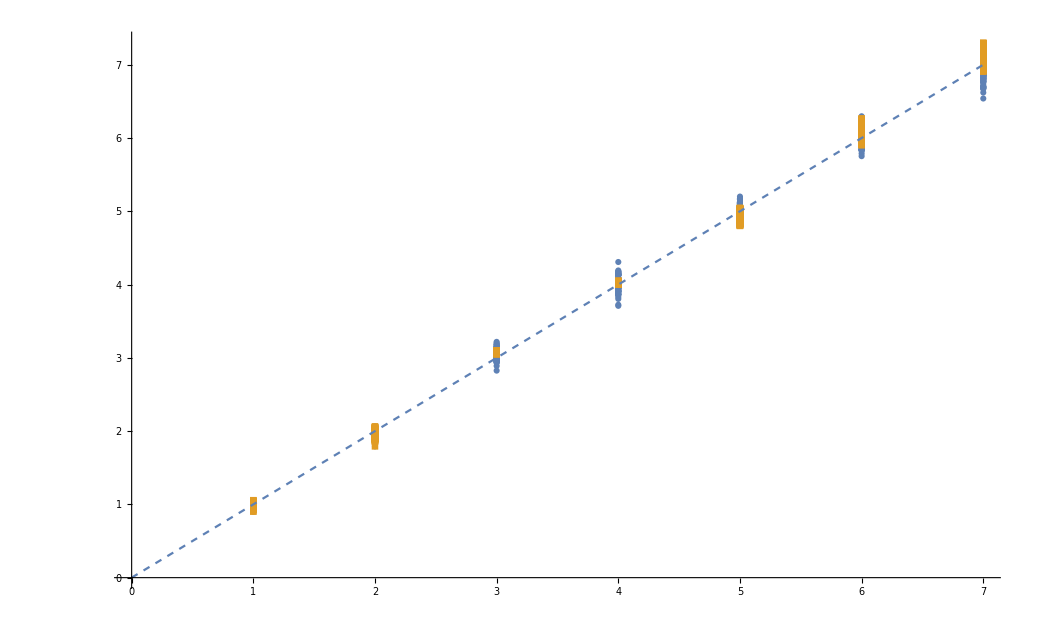

```mathematica
Show[%154,%159]
```

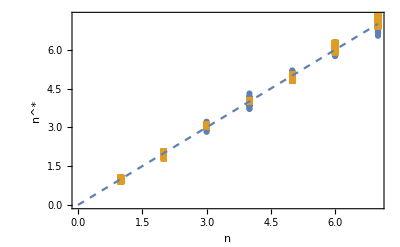

```mathematica
Show[%160,AxesLabel->{HoldForm[n],HoldForm[SuperStar[n]]},PlotLabel->None,LabelStyle->{18,GrayLevel[0]},Frame->True]
```

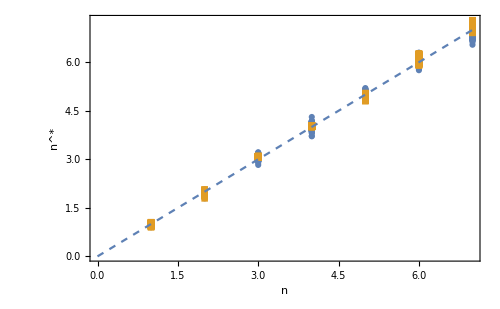

```mathematica
Show[%162,AxesLabel->{None,None},FrameLabel->{{HoldForm[HoldForm[SuperStar[n]]],None},{HoldForm[HoldForm[n]],None}},PlotLabel->None,ImageSize->{500,500}]
```

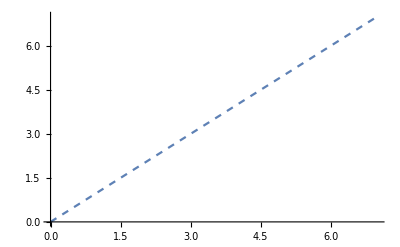

```mathematica
ListLinePlot[Table[{x,x},{x,Range[0,7,0.1]}],PlotStyle->Dashed]
```

```mathematica
Plot[]
```

```mathematica
Transpose[{Table[7,100],Table[RandomReal[{6.9,7.3}],100]}]
```

{{7,7.17556},{7,7.11332},{7,7.13816},{7,7.12748},{7,7.05025},{7,7.20291},{7,6.95069},{7,7.1826},{7,7.25252},{7,7.07963},{7,7.22452},{7,6.96585},{7,7.02291},{7,7.14156},{7,6.92335},{7,7.02548},{7,7.11638},{7,7.29557},{7,7.00873},{7,6.90071},{7,7.10871},{7,7.12551},{7,7.28602},{7,6.90561},{7,7.16092},{7,7.19564},{7,7.05127},{7,6.99708},{7,7.04701},{7,7.01839},{7,7.16012},{7,7.17112},{7,7.16459},{7,7.20472},{7,7.03965},{7,7.03324},{7,6.97443},{7,6.93943},{7,7.09673},{7,7.00298},{7,7.18494},{7,7.01764},{7,6.98915},{7,7.16144},{7,7.20303},{7,7.09514},{7,7.15996},{7,7.03131},{7,7.07478},{7,7.00089},{7,7.07679},{7,7.23915},{7,6.90156},{7,7.01596},{7,7.04892},{7,7.05869},{7,6.96075},{7,7.06708},{7,7.16733},{7,7.27974},{7,6.99133},{7,7.03634},{7,7.22863},{7,7.16299},{7,7.19628},{7,7.13053},{7,7.03754},{7,7.20578},{7,7.17221},{7,7.26037},{7,7.10374},{7,7.28964},{7,7.06992},{7,7.29114},{7,7.28956},{7,7.1053},{7,7.04989},{7,6.94314},{7,7.28771},{7,7.12531},{7,6.97142},{7,7.19599},{7,6.93077},{7,7.19501},{7,7.12138},{7,7.00315},{7,7.154},{7,7.21274},{7,7.25444},{7,7.1377},{7,6.93944},{7,7.2909},{7,7.00902},{7,7.0896},{7,7.25331},{7,7.16985},{7,7.16182},{7,7.0264},{7,7.24741},{7,7.07497}}

```mathematica
Join[Transpose[{Table[7,100],Table[RandomReal[{6.9,7.3}],100]}],Transpose[{Table[6,100],Table[RandomReal[{5.9,6.27}],100]}],Transpose[{Table[5,100],Table[RandomReal[{4.8,5.05}],100]}],Transpose[{Table[4,100],Table[RandomReal[{4,4.05}],100]}],Transpose[{Table[3,100],Table[RandomReal[{3.05,3.1}],100]}],Transpose[{Table[2,100],%98}],Transpose[{Table[1,100],%106}]]
```

{{7,7.16123},{7,7.0004},{7,7.28815},{7,7.21039},{7,7.04363},{7,6.99588},{7,7.24678},{7,7.22157},{7,7.10095},{7,7.17677},{7,7.22584},{7,7.24245},{7,7.14292},{7,7.001},{7,7.17563},{7,7.25079},{7,7.14664},{7,7.2958},{7,6.96886},{7,7.07746},{7,6.95797},{7,7.29169},{7,7.23974},{7,7.06382},{7,7.21599},{7,6.99783},{7,7.0313},{7,7.29897},{7,7.1487},{7,7.27767},{7,7.00859},{7,7.01995},{7,7.13991},{7,6.98944},{7,7.14588},{7,7.05681},{7,7.05127},{7,7.25711},{7,7.17333},{7,7.24645},{7,7.19654},{7,6.9726},{7,7.21657},{7,7.09493},{7,6.989},{7,7.12616},{7,6.93167},{7,7.12277},{7,7.24629},{7,7.0583},{7,7.00811},{7,7.18986},{7,7.20144},{7,7.0602},{7,7.18777},{7,6.98836},{7,7.18345},{7,7.15999},{7,6.92497},{7,7.09761},{7,7.00219},{7,7.07763},{7,7.07222},{7,6.98392},{7,7.13544},{7,6.90732},{7,7.19056},{7,6.98385},{7,6.98985},{7,7.01717},{7,6.95521},{7,7.14049},{7,7.08788},{7,7.28525},{7,7.18314},{7,6.91454},{7,7.08651},{7,7.24371},{7,7.01828},{7,7.28683},{7,7.23135},{7,7.22407},{7,7.29666},{7,6.95091},{7,7.22515},{7,6.99998},{7,6.9081},{7,7.10783},{7,7.24093},{7,7.09593},{7,6.94159},{7,7.13263},{7,6.98082},{7,7.2773},{7,6.925},{7,6.98925},{7,7.21273},{7,7.28512},{7,7.12405},{7,7.173},{6,6.05852},{6,6.00001},{6,5.97084},{6,6.21601},{6,5.90528},{6,6.13041},{6,6.1624},{6,6.24442},{6,6.00876},{6,6.25876},{6,6.08574},{6,6.1351},{6,5.95719},{6,6.19565},{6,6.03128},{6,6.17847},{6,6.12181},{6,6.24512},{6,6.00976},{6,6.14471},{6,6.10024},{6,6.24149},{6,6.14612},{6,6.1935},{6,5.99128},{6,6.1161},{6,5.9692},{6,5.9523},{6,6.25538},{6,6.12903},{6,6.17016},{6,5.94467},{6,6.11683},{6,6.2331},{6,6.17628},{6,6.24909},{6,5.95647},{6,5.98111},{6,5.94733},{6,6.20384},{6,6.08087},{6,6.01098},{6,5.96709},{6,5.93124},{6,6.09088},{6,5.94342},{6,6.04004},{6,6.10286},{6,6.26086},{6,6.21383},{6,5.92356},{6,6.03394},{6,5.92671},{6,6.00394},{6,6.00308},{6,6.07404},{6,6.02433},{6,6.18425},{6,6.26732},{6,6.09539},{6,6.05128},{6,6.08822},{6,6.03712},{6,6.20738},{6,6.23105},{6,6.009},{6,5.99971},{6,6.0165},{6,5.95876},{6,6.04561},{6,6.03723},{6,6.11811},{6,6.24803},{6,6.09587},{6,6.18359},{6,6.07012},{6,6.19779},{6,6.12283},{6,6.00611},{6,6.09286},{6,6.0606},{6,6.17049},{6,5.97976},{6,6.01396},{6,6.09272},{6,6.06014},{6,6.22473},{6,6.02968},{6,6.24465},{6,5.96455},{6,6.02794},{6,5.91467},{6,5.90216},{6,6.09177},{6,6.23127},{6,6.21456},{6,6.01641},{6,6.07269},{6,5.9372},{6,5.9104},{5,4.85005},{5,5.0136},{5,4.81232},{5,4.90281},{5,4.96383},{5,4.80347},{5,5.03183},{5,4.9861},{5,4.86816},{5,5.00965},{5,4.89822},{5,4.83266},{5,4.94278},{5,4.91408},{5,4.94195},{5,4.98294},{5,4.91979},{5,4.92845},{5,4.99953},{5,5.0403},{5,4.86168},{5,4.91524},{5,4.84103},{5,4.87184},{5,4.9863},{5,4.99281},{5,4.96088},{5,5.02649},{5,4.92502},{5,4.82815},{5,4.87249},{5,4.89409},{5,4.94592},{5,4.91234},{5,4.99008},{5,4.87572},{5,4.80048},{5,4.80483},{5,5.02149},{5,4.85376},{5,4.84155},{5,5.04791},{5,5.02121},{5,4.97804},{5,4.89679},{5,4.98224},{5,4.99626},{5,4.90628},{5,4.82695},{5,4.97187},{5,4.95234},{5,4.84029},{5,4.93107},{5,4.92788},{5,5.03865},{5,4.87948},{5,5.0272},{5,5.02573},{5,5.03791},{5,4.8871},{5,4.9627},{5,4.8289},{5,4.87912},{5,4.82377},{5,4.8292},{5,4.98371},{5,4.86425},{5,4.93192},{5,4.96515},{5,4.99137},{5,4.84779},{5,4.82528},{5,4.88514},{5,4.95609},{5,4.8255},{5,4.89551},{5,4.96971},{5,4.98838},{5,4.8355},{5,5.03825},{5,4.86663},{5,4.97883},{5,4.96032},{5,5.02628},{5,4.91404},{5,4.8798},{5,4.9314},{5,5.03408},{5,4.81772},{5,4.82863},{5,4.81416},{5,5.02161},{5,4.83468},{5,5.01733},{5,4.93082},{5,4.89751},{5,5.01959},{5,5.01573},{5,5.04022},{5,5.03066},{4,4.02671},{4,4.0095},{4,4.04207},{4,4.02073},{4,4.03269},{4,4.01763},{4,4.0355},{4,4.00229},{4,4.04112},{4,4.04783},{4,4.00855},{4,4.00064},{4,4.02415},{4,4.00742},{4,4.02172},{4,4.01275},{4,4.03903},{4,4.01559},{4,4.02283},{4,4.01584},{4,4.0023},{4,4.01623},{4,4.03648},{4,4.04423},{4,4.00166},{4,4.02659},{4,4.00432},{4,4.03233},{4,4.02702},{4,4.04695},{4,4.00755},{4,4.00899},{4,4.00095},{4,4.01645},{4,4.02992},{4,4.01486},{4,4.00978},{4,4.04614},{4,4.00099},{4,4.04228},{4,4.03766},{4,4.02464},{4,4.0081},{4,4.01904},{4,4.03078},{4,4.01649},{4,4.02065},{4,4.02847},{4,4.03932},{4,4.03198},{4,4.01161},{4,4.03241},{4,4.04546},{4,4.0168},{4,4.00966},{4,4.03745},{4,4.04556},{4,4.01733},{4,4.00317},{4,4.01053},{4,4.01732},{4,4.00639},{4,4.02149},{4,4.0496},{4,4.01342},{4,4.01688},{4,4.01299},{4,4.00178},{4,4.04203},{4,4.01631},{4,4.02468},{4,4.02698},{4,4.02891},{4,4.03612},{4,4.00188},{4,4.04405},{4,4.02448},{4,4.02483},{4,4.02296},{4,4.00261},{4,4.0405},{4,4.01302},{4,4.01122},{4,4.0143},{4,4.02207},{4,4.03963},{4,4.021},{4,4.00285},{4,4.04915},{4,4.01193},{4,4.02453},{4,4.01131},{4,4.03977},{4,4.04036},{4,4.01509},{4,4.02568},{4,4.04944},{4,4.04111},{4,4.03039},{4,4.00935},{3,3.09771},{3,3.06168},{3,3.06767},{3,3.07702},{3,3.06804},{3,3.08887},{3,3.07905},{3,3.06946},{3,3.07812},{3,3.09063},{3,3.07668},{3,3.06287},{3,3.07436},{3,3.06769},{3,3.08655},{3,3.05968},{3,3.09271},{3,3.08656},{3,3.09191},{3,3.06981},{3,3.07503},{3,3.05928},{3,3.07023},{3,3.07172},{3,3.08239},{3,3.06695},{3,3.09835},{3,3.06583},{3,3.07439},{3,3.05047},{3,3.05482},{3,3.07934},{3,3.07789},{3,3.06831},{3,3.0817},{3,3.05826},{3,3.08314},{3,3.08564},{3,3.08987},{3,3.08009},{3,3.05588},{3,3.06243},{3,3.08482},{3,3.06754},{3,3.06396},{3,3.09247},{3,3.07664},{3,3.06349},{3,3.08908},{3,3.08178},{3,3.07609},{3,3.09684},{3,3.08709},{3,3.05769},{3,3.06416},{3,3.09083},{3,3.08968},{3,3.07829},{3,3.06175},{3,3.05553},{3,3.06454},{3,3.0776},{3,3.09139},{3,3.06935},{3,3.05264},{3,3.05389},{3,3.067},{3,3.06034},{3,3.09546},{3,3.07901},{3,3.0703},{3,3.09724},{3,3.06067},{3,3.06768},{3,3.07195},{3,3.0511},{3,3.06701},{3,3.07024},{3,3.07482},{3,3.09244},{3,3.06417},{3,3.09413},{3,3.07028},{3,3.08302},{3,3.09782},{3,3.06029},{3,3.08743},{3,3.06404},{3,3.09734},{3,3.09106},{3,3.08999},{3,3.06661},{3,3.07968},{3,3.0908},{3,3.06715},{3,3.07869},{3,3.09673},{3,3.07367},{3,3.05076},{3,3.06206},{2,1.91786},{2,1.945},{2,1.9753},{2,1.94026},{2,1.95569},{2,1.87674},{2,1.89217},{2,2.04061},{2,1.97471},{2,2.00934},{2,2.0144},{2,1.95077},{2,2.00647},{2,1.85485},{2,1.98537},{2,2.01399},{2,1.92437},{2,1.92887},{2,1.99507},{2,1.93182},{2,2.0024},{2,1.98542},{2,1.89845},{2,1.88492},{2,1.94962},{2,1.8959},{2,1.92772},{2,1.92441},{2,2.0252},{2,1.91056},{2,1.95368},{2,2.03782},{2,2.03269},{2,1.97588},{2,1.99555},{2,2.00605},{2,1.86606},{2,1.98827},{2,2.0487},{2,1.95363},{2,2.05505},{2,1.96992},{2,1.9417},{2,1.8977},{2,2.05215},{2,1.93165},{2,1.99851},{2,1.92479},{2,1.94199},{2,1.91314},{2,1.99098},{2,1.94893},{2,1.87743},{2,1.93758},{2,1.98093},{2,1.93824},{2,1.96353},{2,1.8899},{2,2.03769},{2,1.99574},{2,1.91326},{2,1.98945},{2,2.0539},{2,1.91489},{2,1.96762},{2,1.88467},{2,2.02165},{2,2.02654},{2,1.93191},{2,1.97672},{2,2.00814},{2,1.97109},{2,2.04632},{2,2.00414},{2,1.93579},{2,1.87377},{2,1.96266},{2,1.90823},{2,1.95305},{2,1.90565},{2,1.90127},{2,1.89436},{2,1.95108},{2,1.93951},{2,1.95672},{2,1.93546},{2,1.96906},{2,2.06482},{2,1.93803},{2,2.02446},{2,1.90023},{2,1.96019},{2,1.79173},{2,1.974},{2,1.90217},{2,1.93946},{2,2.01387},{2,1.94113},{2,1.9919},{2,1.92748},{1,0.950351},{1,1.01597},{1,0.934718},{1,0.991504},{1,0.960947},{1,1.02427},{1,0.942185},{1,1.02371},{1,0.981148},{1,0.988685},{1,0.991282},{1,0.98086},{1,0.996144},{1,1.05487},{1,0.94577},{1,1.00203},{1,1.00848},{1,0.95668},{1,0.946802},{1,0.962424},{1,0.950591},{1,1.04384},{1,0.994494},{1,1.00076},{1,0.927544},{1,1.01426},{1,0.99654},{1,0.960233},{1,0.974079},{1,0.96235},{1,0.925196},{1,1.00342},{1,1.04943},{1,0.997243},{1,0.943337},{1,0.970586},{1,0.948313},{1,0.974474},{1,0.986183},{1,0.903073},{1,1.02857},{1,0.996471},{1,0.983773},{1,0.987539},{1,0.975996},{1,0.945262},{1,0.952492},{1,1.0466},{1,0.987967},{1,0.982405},{1,1.01427},{1,0.974758},{1,0.998835},{1,0.943763},{1,1.03395},{1,1.01083},{1,1.01167},{1,0.987699},{1,0.941445},{1,1.00224},{1,1.01025},{1,0.999885},{1,0.979226},{1,0.942426},{1,1.01637},{1,0.97196},{1,0.96164},{1,0.989155},{1,0.975583},{1,0.993192},{1,0.989128},{1,0.974007},{1,1.01145},{1,1.00132},{1,1.00237},{1,1.05696},{1,0.97694},{1,0.993771},{1,0.928883},{1,1.02622},{1,1.00643},{1,0.98988},{1,0.984498},{1,1.02567},{1,0.994262},{1,0.996802},{1,0.97952},{1,0.949644},{1,0.951387},{1,0.983626},{1,0.979198},{1,0.902628},{1,0.979749},{1,0.987082},{1,0.988437},{1,1.02989},{1,1.03678},{1,1.02476},{1,0.937575},{1,1.01661}}

```mathematica
Table[intg[0.9,1.5,λ],{λ,100}]
```

{7.07825,6.53935,6.96204,6.9192,6.94095,6.86543,7.16141,7.07584,7.13687,6.97366,7.08807,6.7787,7.06651,6.84439,7.06638,6.83839,6.96583,6.80481,6.82808,6.6912,6.84719,6.92799,7.08603,6.89628,6.85138,7.00275,6.76583,6.87358,6.87174,7.01025,6.70537,6.66912,6.68407,7.04182,6.78948,6.70495,6.93661,6.87074,6.82533,6.86065,7.04607,6.88926,6.9463,6.89649,7.15753,6.85779,6.9414,6.97977,7.05469,6.90211,6.97505,6.92337,6.80402,6.70226,6.68162,6.82139,6.94494,7.08026,6.93596,6.73716,6.87172,6.9621,7.0217,7.06202,6.76706,7.09574,6.8174,6.91751,6.68467,6.8943,6.8818,6.84923,6.89223,6.8889,6.80086,6.88824,6.91253,6.93599,6.88153,6.95782,6.78144,6.99948,6.96187,7.03604,7.03201,7.02904,6.88119,6.91166,6.62052,6.94546,6.8803,6.82518,6.8892,6.85434,6.81006,6.76543,7.06088,6.8513,7.13813,7.04847}

```mathematica
Import["6imppoi.dat"]
```

{{6.12555},{6.26514},{5.92818},{6.03313},{5.95201},{6.03502},{6.06434},{5.82361},{6.23969},{6.10335},{6.07553},{6.03243},{6.16288},{6.06536},{5.99633},{6.00033},{6.11281},{6.02479},{6.00611},{5.85925},{5.8461},{5.88507},{6.01672},{5.84072},{6.01959},{6.00502},{6.11205},{6.01062},{6.06377},{5.95565},{6.09998},{6.29698},{5.83896},{6.03958},{6.03951},{5.94342},{5.9727},{6.01477},{5.91905},{5.9769},{5.998},{5.98179},{5.75244},{5.88456},{6.02668},{5.95983},{6.01148},{5.94988},{6.09948},{5.88714},{6.01575},{5.92145},{5.92397},{5.93783},{5.97937},{5.99439},{6.13902},{5.95961},{6.08194},{6.00151},{5.84119},{6.07206},{6.03414},{5.91467},{6.1563},{6.06842},{6.07152},{5.89674},{6.08445},{6.00792},{5.78854},{5.92672},{6.0432},{6.07062},{5.97701},{5.92096},{5.91498},{5.95779},{5.91103},{5.84623},{6.14261},{5.97987},{6.08964},{6.10847},{5.99127},{5.98823},{5.83923},{6.14637},{6.08906},{5.9393},{6.13106},{6.03914},{6.23913},{5.9436},{6.2493},{6.00122},{6.17588},{6.02124},{6.08132},{6.0237}}

```mathematica
Flatten[%120]
```

{6.12555,6.26514,5.92818,6.03313,5.95201,6.03502,6.06434,5.82361,6.23969,6.10335,6.07553,6.03243,6.16288,6.06536,5.99633,6.00033,6.11281,6.02479,6.00611,5.85925,5.8461,5.88507,6.01672,5.84072,6.01959,6.00502,6.11205,6.01062,6.06377,5.95565,6.09998,6.29698,5.83896,6.03958,6.03951,5.94342,5.9727,6.01477,5.91905,5.9769,5.998,5.98179,5.75244,5.88456,6.02668,5.95983,6.01148,5.94988,6.09948,5.88714,6.01575,5.92145,5.92397,5.93783,5.97937,5.99439,6.13902,5.95961,6.08194,6.00151,5.84119,6.07206,6.03414,5.91467,6.1563,6.06842,6.07152,5.89674,6.08445,6.00792,5.78854,5.92672,6.0432,6.07062,5.97701,5.92096,5.91498,5.95779,5.91103,5.84623,6.14261,5.97987,6.08964,6.10847,5.99127,5.98823,5.83923,6.14637,6.08906,5.9393,6.13106,6.03914,6.23913,5.9436,6.2493,6.00122,6.17588,6.02124,6.08132,6.0237}

```mathematica
Table[intg[0.9,1.5,λ],{λ,100}]
```

{5.0021,5.01626,4.93655,5.20099,5.08139,5.01603,4.98659,5.05049,4.99174,5.07249,4.85145,5.06829,4.9275,5.1645,5.01197,4.96105,5.08534,5.12923,5.06089,5.11108,4.96735,4.9015,5.0411,4.87599,5.02622,4.94936,5.01957,5.00002,5.05533,4.92985,5.02522,5.04209,5.11067,4.83263,5.113,5.0236,4.83719,4.87919,4.89421,5.12463,4.95932,4.98548,5.09982,5.10091,4.89221,4.99286,5.04412,5.16865,4.88392,5.04867,4.90787,5.09726,4.93135,5.03181,4.99989,4.90943,5.06304,5.05079,5.09269,4.86077,4.90179,4.97286,5.03661,5.05332,4.99499,5.09267,5.04909,5.02978,4.92514,4.89659,5.02373,4.9569,4.90991,4.98744,4.85339,4.90825,5.01758,4.84705,4.84339,4.93228,5.12057,4.97127,5.01594,5.0459,4.91348,5.02531,5.03987,5.04276,4.85334,5.08209,4.95416,4.83027,5.0441,5.05998,5.10827,4.88276,5.04878,5.11623,5.16933,5.0483}

```mathematica
Table[intg[0.9,1.5,λ],{λ,100}]
```

{0.950351,1.01597,0.934718,0.991504,0.960947,1.02427,0.942185,1.02371,0.981148,0.988685,0.991282,0.98086,0.996144,1.05487,0.94577,1.00203,1.00848,0.95668,0.946802,0.962424,0.950591,1.04384,0.994494,1.00076,0.927544,1.01426,0.99654,0.960233,0.974079,0.96235,0.925196,1.00342,1.04943,0.997243,0.943337,0.970586,0.948313,0.974474,0.986183,0.903073,1.02857,0.996471,0.983773,0.987539,0.975996,0.945262,0.952492,1.0466,0.987967,0.982405,1.01427,0.974758,0.998835,0.943763,1.03395,1.01083,1.01167,0.987699,0.941445,1.00224,1.01025,0.999885,0.979226,0.942426,1.01637,0.97196,0.96164,0.989155,0.975583,0.993192,0.989128,0.974007,1.01145,1.00132,1.00237,1.05696,0.97694,0.993771,0.928883,1.02622,1.00643,0.98988,0.984498,1.02567,0.994262,0.996802,0.97952,0.949644,0.951387,0.983626,0.979198,0.902628,0.979749,0.987082,0.988437,1.02989,1.03678,1.02476,0.937575,1.01661}

```mathematica
Table[intg[0.9,1.5,λ],{λ,100}]
```

{1.91786,1.945,1.9753,1.94026,1.95569,1.87674,1.89217,2.04061,1.97471,2.00934,2.0144,1.95077,2.00647,1.85485,1.98537,2.01399,1.92437,1.92887,1.99507,1.93182,2.0024,1.98542,1.89845,1.88492,1.94962,1.8959,1.92772,1.92441,2.0252,1.91056,1.95368,2.03782,2.03269,1.97588,1.99555,2.00605,1.86606,1.98827,2.0487,1.95363,2.05505,1.96992,1.9417,1.8977,2.05215,1.93165,1.99851,1.92479,1.94199,1.91314,1.99098,1.94893,1.87743,1.93758,1.98093,1.93824,1.96353,1.8899,2.03769,1.99574,1.91326,1.98945,2.0539,1.91489,1.96762,1.88467,2.02165,2.02654,1.93191,1.97672,2.00814,1.97109,2.04632,2.00414,1.93579,1.87377,1.96266,1.90823,1.95305,1.90565,1.90127,1.89436,1.95108,1.93951,1.95672,1.93546,1.96906,2.06482,1.93803,2.02446,1.90023,1.96019,1.79173,1.974,1.90217,1.93946,2.01387,1.94113,1.9919,1.92748}

```mathematica
Table[intg[0.9,1.5,λ],{λ,100}]
```

{3.04423,3.14959,2.95542,3.10666,3.0278,3.03809,2.97196,3.05313,3.15865,3.21791,3.01449,2.95109,3.14227,3.14412,3.1048,2.94087,2.89005,3.0691,2.98228,3.20103,3.12031,2.98528,2.93075,3.10186,3.05051,3.05555,3.02155,3.06346,2.94263,3.05488,3.09406,2.95815,3.04967,2.96873,3.0136,3.08522,3.08052,3.12784,3.10075,2.99206,3.11349,2.97853,3.08947,3.04191,3.18155,3.07082,2.984,3.03196,2.96752,3.05302,3.05646,3.09017,2.9639,3.09814,3.03122,3.06235,2.99208,3.137,3.01242,3.12253,3.10671,3.04702,3.08647,2.82565,3.00847,3.05972,3.03164,3.02434,3.14492,3.05555,3.09658,3.18072,3.08129,3.06064,3.08213,3.04818,3.04753,3.0264,3.08969,3.05581,2.9813,2.98181,3.04182,3.127,3.06083,3.02537,3.02452,2.98483,3.05962,2.94756,3.01692,2.9975,3.00659,3.07004,3.17638,3.04728,3.14405,3.04269,3.03479,3.12656}

```mathematica
Table[intg[0.9,1.5,λ],{λ,100}]
```

{3.96046,4.05121,4.06398,4.07735,4.00293,4.03482,4.03079,4.04097,4.0515,4.00354,4.04823,4.12955,4.01643,3.9694,4.04203,4.08465,3.87083,3.9951,4.14747,3.80406,3.83047,3.97832,3.96793,4.03391,3.97503,3.98171,3.93055,4.05283,3.97479,4.04042,4.05168,4.06719,3.9528,4.03631,4.08743,4.03893,4.0368,4.05152,3.99295,4.01062,4.17398,3.94894,4.15825,4.13491,4.12195,4.19223,4.13186,4.18117,4.08239,3.9083,3.85719,4.16023,4.17176,3.98384,4.07989,3.97916,4.06169,3.86116,3.97072,3.98109,3.99632,3.98357,4.13387,3.89647,3.93642,4.01733,4.07253,4.02913,4.14589,4.05524,3.89299,3.72452,3.91267,3.9499,4.07102,3.97801,4.07009,3.87028,3.99908,4.05554,3.90514,4.13162,4.30785,4.14341,4.0425,3.869,4.00175,3.70974,3.91751,4.05741,4.05609,3.91696,3.95449,4.02505,4.06867,3.95103,4.1296,4.08146,4.0759,3.90943}

```mathematica
Join[{1,%106}]
```

{1,{0.950351,1.01597,0.934718,0.991504,0.960947,1.02427,0.942185,1.02371,0.981148,0.988685,0.991282,0.98086,0.996144,1.05487,0.94577,1.00203,1.00848,0.95668,0.946802,0.962424,0.950591,1.04384,0.994494,1.00076,0.927544,1.01426,0.99654,0.960233,0.974079,0.96235,0.925196,1.00342,1.04943,0.997243,0.943337,0.970586,0.948313,0.974474,0.986183,0.903073,1.02857,0.996471,0.983773,0.987539,0.975996,0.945262,0.952492,1.0466,0.987967,0.982405,1.01427,0.974758,0.998835,0.943763,1.03395,1.01083,1.01167,0.987699,0.941445,1.00224,1.01025,0.999885,0.979226,0.942426,1.01637,0.97196,0.96164,0.989155,0.975583,0.993192,0.989128,0.974007,1.01145,1.00132,1.00237,1.05696,0.97694,0.993771,0.928883,1.02622,1.00643,0.98988,0.984498,1.02567,0.994262,0.996802,0.97952,0.949644,0.951387,0.983626,0.979198,0.902628,0.979749,0.987082,0.988437,1.02989,1.03678,1.02476,0.937575,1.01661}}

```mathematica
Join[%73,%90,%98,%90,%106,%114,%132,%131]
```

{3.96046,4.05121,4.06398,4.07735,4.00293,4.03482,4.03079,4.04097,4.0515,4.00354,4.04823,4.12955,4.01643,3.9694,4.04203,4.08465,3.87083,3.9951,4.14747,3.80406,3.83047,3.97832,3.96793,4.03391,3.97503,3.98171,3.93055,4.05283,3.97479,4.04042,4.05168,4.06719,3.9528,4.03631,4.08743,4.03893,4.0368,4.05152,3.99295,4.01062,4.17398,3.94894,4.15825,4.13491,4.12195,4.19223,4.13186,4.18117,4.08239,3.9083,3.85719,4.16023,4.17176,3.98384,4.07989,3.97916,4.06169,3.86116,3.97072,3.98109,3.99632,3.98357,4.13387,3.89647,3.93642,4.01733,4.07253,4.02913,4.14589,4.05524,3.89299,3.72452,3.91267,3.9499,4.07102,3.97801,4.07009,3.87028,3.99908,4.05554,3.90514,4.13162,4.30785,4.14341,4.0425,3.869,4.00175,3.70974,3.91751,4.05741,4.05609,3.91696,3.95449,4.02505,4.06867,3.95103,4.1296,4.08146,4.0759,3.90943,3.04423,3.14959,2.95542,3.10666,3.0278,3.03809,2.97196,3.05313,3.15865,3.21791,3.01449,2.95109,3.14227,3.14412,3.1048,2.94087,2.89005,3.0691,2.98228,3.20103,3.12031,2.98528,2.93075,3.10186,3.05051,3.05555,3.02155,3.06346,2.94263,3.05488,3.09406,2.95815,3.04967,2.96873,3.0136,3.08522,3.08052,3.12784,3.10075,2.99206,3.11349,2.97853,3.08947,3.04191,3.18155,3.07082,2.984,3.03196,2.96752,3.05302,3.05646,3.09017,2.9639,3.09814,3.03122,3.06235,2.99208,3.137,3.01242,3.12253,3.10671,3.04702,3.08647,2.82565,3.00847,3.05972,3.03164,3.02434,3.14492,3.05555,3.09658,3.18072,3.08129,3.06064,3.08213,3.04818,3.04753,3.0264,3.08969,3.05581,2.9813,2.98181,3.04182,3.127,3.06083,3.02537,3.02452,2.98483,3.05962,2.94756,3.01692,2.9975,3.00659,3.07004,3.17638,3.04728,3.14405,3.04269,3.03479,3.12656,1.91786,1.945,1.9753,1.94026,1.95569,1.87674,1.89217,2.04061,1.97471,2.00934,2.0144,1.95077,2.00647,1.85485,1.98537,2.01399,1.92437,1.92887,1.99507,1.93182,2.0024,1.98542,1.89845,1.88492,1.94962,1.8959,1.92772,1.92441,2.0252,1.91056,1.95368,2.03782,2.03269,1.97588,1.99555,2.00605,1.86606,1.98827,2.0487,1.95363,2.05505,1.96992,1.9417,1.8977,2.05215,1.93165,1.99851,1.92479,1.94199,1.91314,1.99098,1.94893,1.87743,1.93758,1.98093,1.93824,1.96353,1.8899,2.03769,1.99574,1.91326,1.98945,2.0539,1.91489,1.96762,1.88467,2.02165,2.02654,1.93191,1.97672,2.00814,1.97109,2.04632,2.00414,1.93579,1.87377,1.96266,1.90823,1.95305,1.90565,1.90127,1.89436,1.95108,1.93951,1.95672,1.93546,1.96906,2.06482,1.93803,2.02446,1.90023,1.96019,1.79173,1.974,1.90217,1.93946,2.01387,1.94113,1.9919,1.92748,3.04423,3.14959,2.95542,3.10666,3.0278,3.03809,2.97196,3.05313,3.15865,3.21791,3.01449,2.95109,3.14227,3.14412,3.1048,2.94087,2.89005,3.0691,2.98228,3.20103,3.12031,2.98528,2.93075,3.10186,3.05051,3.05555,3.02155,3.06346,2.94263,3.05488,3.09406,2.95815,3.04967,2.96873,3.0136,3.08522,3.08052,3.12784,3.10075,2.99206,3.11349,2.97853,3.08947,3.04191,3.18155,3.07082,2.984,3.03196,2.96752,3.05302,3.05646,3.09017,2.9639,3.09814,3.03122,3.06235,2.99208,3.137,3.01242,3.12253,3.10671,3.04702,3.08647,2.82565,3.00847,3.05972,3.03164,3.02434,3.14492,3.05555,3.09658,3.18072,3.08129,3.06064,3.08213,3.04818,3.04753,3.0264,3.08969,3.05581,2.9813,2.98181,3.04182,3.127,3.06083,3.02537,3.02452,2.98483,3.05962,2.94756,3.01692,2.9975,3.00659,3.07004,3.17638,3.04728,3.14405,3.04269,3.03479,3.12656,0.950351,1.01597,0.934718,0.991504,0.960947,1.02427,0.942185,1.02371,0.981148,0.988685,0.991282,0.98086,0.996144,1.05487,0.94577,1.00203,1.00848,0.95668,0.946802,0.962424,0.950591,1.04384,0.994494,1.00076,0.927544,1.01426,0.99654,0.960233,0.974079,0.96235,0.925196,1.00342,1.04943,0.997243,0.943337,0.970586,0.948313,0.974474,0.986183,0.903073,1.02857,0.996471,0.983773,0.987539,0.975996,0.945262,0.952492,1.0466,0.987967,0.982405,1.01427,0.974758,0.998835,0.943763,1.03395,1.01083,1.01167,0.987699,0.941445,1.00224,1.01025,0.999885,0.979226,0.942426,1.01637,0.97196,0.96164,0.989155,0.975583,0.993192,0.989128,0.974007,1.01145,1.00132,1.00237,1.05696,0.97694,0.993771,0.928883,1.02622,1.00643,0.98988,0.984498,1.02567,0.994262,0.996802,0.97952,0.949644,0.951387,0.983626,0.979198,0.902628,0.979749,0.987082,0.988437,1.02989,1.03678,1.02476,0.937575,1.01661,5.0021,5.01626,4.93655,5.20099,5.08139,5.01603,4.98659,5.05049,4.99174,5.07249,4.85145,5.06829,4.9275,5.1645,5.01197,4.96105,5.08534,5.12923,5.06089,5.11108,4.96735,4.9015,5.0411,4.87599,5.02622,4.94936,5.01957,5.00002,5.05533,4.92985,5.02522,5.04209,5.11067,4.83263,5.113,5.0236,4.83719,4.87919,4.89421,5.12463,4.95932,4.98548,5.09982,5.10091,4.89221,4.99286,5.04412,5.16865,4.88392,5.04867,4.90787,5.09726,4.93135,5.03181,4.99989,4.90943,5.06304,5.05079,5.09269,4.86077,4.90179,4.97286,5.03661,5.05332,4.99499,5.09267,5.04909,5.02978,4.92514,4.89659,5.02373,4.9569,4.90991,4.98744,4.85339,4.90825,5.01758,4.84705,4.84339,4.93228,5.12057,4.97127,5.01594,5.0459,4.91348,5.02531,5.03987,5.04276,4.85334,5.08209,4.95416,4.83027,5.0441,5.05998,5.10827,4.88276,5.04878,5.11623,5.16933,5.0483,7.07825,6.53935,6.96204,6.9192,6.94095,6.86543,7.16141,7.07584,7.13687,6.97366,7.08807,6.7787,7.06651,6.84439,7.06638,6.83839,6.96583,6.80481,6.82808,6.6912,6.84719,6.92799,7.08603,6.89628,6.85138,7.00275,6.76583,6.87358,6.87174,7.01025,6.70537,6.66912,6.68407,7.04182,6.78948,6.70495,6.93661,6.87074,6.82533,6.86065,7.04607,6.88926,6.9463,6.89649,7.15753,6.85779,6.9414,6.97977,7.05469,6.90211,6.97505,6.92337,6.80402,6.70226,6.68162,6.82139,6.94494,7.08026,6.93596,6.73716,6.87172,6.9621,7.0217,7.06202,6.76706,7.09574,6.8174,6.91751,6.68467,6.8943,6.8818,6.84923,6.89223,6.8889,6.80086,6.88824,6.91253,6.93599,6.88153,6.95782,6.78144,6.99948,6.96187,7.03604,7.03201,7.02904,6.88119,6.91166,6.62052,6.94546,6.8803,6.82518,6.8892,6.85434,6.81006,6.76543,7.06088,6.8513,7.13813,7.04847,6.12555,6.26514,5.92818,6.03313,5.95201,6.03502,6.06434,5.82361,6.23969,6.10335,6.07553,6.03243,6.16288,6.06536,5.99633,6.00033,6.11281,6.02479,6.00611,5.85925,5.8461,5.88507,6.01672,5.84072,6.01959,6.00502,6.11205,6.01062,6.06377,5.95565,6.09998,6.29698,5.83896,6.03958,6.03951,5.94342,5.9727,6.01477,5.91905,5.9769,5.998,5.98179,5.75244,5.88456,6.02668,5.95983,6.01148,5.94988,6.09948,5.88714,6.01575,5.92145,5.92397,5.93783,5.97937,5.99439,6.13902,5.95961,6.08194,6.00151,5.84119,6.07206,6.03414,5.91467,6.1563,6.06842,6.07152,5.89674,6.08445,6.00792,5.78854,5.92672,6.0432,6.07062,5.97701,5.92096,5.91498,5.95779,5.91103,5.84623,6.14261,5.97987,6.08964,6.10847,5.99127,5.98823,5.83923,6.14637,6.08906,5.9393,6.13106,6.03914,6.23913,5.9436,6.2493,6.00122,6.17588,6.02124,6.08132,6.0237}

```mathematica
Sort[%136]
```

{0.902628,0.903073,0.925196,0.927544,0.928883,0.934718,0.937575,0.941445,0.942185,0.942426,0.943337,0.943763,0.945262,0.94577,0.946802,0.948313,0.949644,0.950351,0.950591,0.951387,0.952492,0.95668,0.960233,0.960947,0.96164,0.96235,0.962424,0.970586,0.97196,0.974007,0.974079,0.974474,0.974758,0.975583,0.975996,0.97694,0.979198,0.979226,0.97952,0.979749,0.98086,0.981148,0.982405,0.983626,0.983773,0.984498,0.986183,0.987082,0.987539,0.987699,0.987967,0.988437,0.988685,0.989128,0.989155,0.98988,0.991282,0.991504,0.993192,0.993771,0.994262,0.994494,0.996144,0.996471,0.99654,0.996802,0.997243,0.998835,0.999885,1.00076,1.00132,1.00203,1.00224,1.00237,1.00342,1.00643,1.00848,1.01025,1.01083,1.01145,1.01167,1.01426,1.01427,1.01597,1.01637,1.01661,1.02371,1.02427,1.02476,1.02567,1.02622,1.02857,1.02989,1.03395,1.03678,1.04384,1.0466,1.04943,1.05487,1.05696,1.79173,1.85485,1.86606,1.87377,1.87674,1.87743,1.88467,1.88492,1.8899,1.89217,1.89436,1.8959,1.8977,1.89845,1.90023,1.90127,1.90217,1.90565,1.90823,1.91056,1.91314,1.91326,1.91489,1.91786,1.92437,1.92441,1.92479,1.92748,1.92772,1.92887,1.93165,1.93182,1.93191,1.93546,1.93579,1.93758,1.93803,1.93824,1.93946,1.93951,1.94026,1.94113,1.9417,1.94199,1.945,1.94893,1.94962,1.95077,1.95108,1.95305,1.95363,1.95368,1.95569,1.95672,1.96019,1.96266,1.96353,1.96762,1.96906,1.96992,1.97109,1.974,1.97471,1.9753,1.97588,1.97672,1.98093,1.98537,1.98542,1.98827,1.98945,1.99098,1.9919,1.99507,1.99555,1.99574,1.99851,2.0024,2.00414,2.00605,2.00647,2.00814,2.00934,2.01387,2.01399,2.0144,2.02165,2.02446,2.0252,2.02654,2.03269,2.03769,2.03782,2.04061,2.04632,2.0487,2.05215,2.0539,2.05505,2.06482,2.82565,2.82565,2.89005,2.89005,2.93075,2.93075,2.94087,2.94087,2.94263,2.94263,2.94756,2.94756,2.95109,2.95109,2.95542,2.95542,2.95815,2.95815,2.9639,2.9639,2.96752,2.96752,2.96873,2.96873,2.97196,2.97196,2.97853,2.97853,2.9813,2.9813,2.98181,2.98181,2.98228,2.98228,2.984,2.984,2.98483,2.98483,2.98528,2.98528,2.99206,2.99206,2.99208,2.99208,2.9975,2.9975,3.00659,3.00659,3.00847,3.00847,3.01242,3.01242,3.0136,3.0136,3.01449,3.01449,3.01692,3.01692,3.02155,3.02155,3.02434,3.02434,3.02452,3.02452,3.02537,3.02537,3.0264,3.0264,3.0278,3.0278,3.03122,3.03122,3.03164,3.03164,3.03196,3.03196,3.03479,3.03479,3.03809,3.03809,3.04182,3.04182,3.04191,3.04191,3.04269,3.04269,3.04423,3.04423,3.04702,3.04702,3.04728,3.04728,3.04753,3.04753,3.04818,3.04818,3.04967,3.04967,3.05051,3.05051,3.05302,3.05302,3.05313,3.05313,3.05488,3.05488,3.05555,3.05555,3.05555,3.05555,3.05581,3.05581,3.05646,3.05646,3.05962,3.05962,3.05972,3.05972,3.06064,3.06064,3.06083,3.06083,3.06235,3.06235,3.06346,3.06346,3.0691,3.0691,3.07004,3.07004,3.07082,3.07082,3.08052,3.08052,3.08129,3.08129,3.08213,3.08213,3.08522,3.08522,3.08647,3.08647,3.08947,3.08947,3.08969,3.08969,3.09017,3.09017,3.09406,3.09406,3.09658,3.09658,3.09814,3.09814,3.10075,3.10075,3.10186,3.10186,3.1048,3.1048,3.10666,3.10666,3.10671,3.10671,3.11349,3.11349,3.12031,3.12031,3.12253,3.12253,3.12656,3.12656,3.127,3.127,3.12784,3.12784,3.137,3.137,3.14227,3.14227,3.14405,3.14405,3.14412,3.14412,3.14492,3.14492,3.14959,3.14959,3.15865,3.15865,3.17638,3.17638,3.18072,3.18072,3.18155,3.18155,3.20103,3.20103,3.21791,3.21791,3.70974,3.72452,3.80406,3.83047,3.85719,3.86116,3.869,3.87028,3.87083,3.89299,3.89647,3.90514,3.9083,3.90943,3.91267,3.91696,3.91751,3.93055,3.93642,3.94894,3.9499,3.95103,3.9528,3.95449,3.96046,3.96793,3.9694,3.97072,3.97479,3.97503,3.97801,3.97832,3.97916,3.98109,3.98171,3.98357,3.98384,3.99295,3.9951,3.99632,3.99908,4.00175,4.00293,4.00354,4.01062,4.01643,4.01733,4.02505,4.02913,4.03079,4.03391,4.03482,4.03631,4.0368,4.03893,4.04042,4.04097,4.04203,4.0425,4.04823,4.05121,4.0515,4.05152,4.05168,4.05283,4.05524,4.05554,4.05609,4.05741,4.06169,4.06398,4.06719,4.06867,4.07009,4.07102,4.07253,4.0759,4.07735,4.07989,4.08146,4.08239,4.08465,4.08743,4.12195,4.12955,4.1296,4.13162,4.13186,4.13387,4.13491,4.14341,4.14589,4.14747,4.15825,4.16023,4.17176,4.17398,4.18117,4.19223,4.30785,4.83027,4.83263,4.83719,4.84339,4.84705,4.85145,4.85334,4.85339,4.86077,4.87599,4.87919,4.88276,4.88392,4.89221,4.89421,4.89659,4.9015,4.90179,4.90787,4.90825,4.90943,4.90991,4.91348,4.92514,4.9275,4.92985,4.93135,4.93228,4.93655,4.94936,4.95416,4.9569,4.95932,4.96105,4.96735,4.97127,4.97286,4.98548,4.98659,4.98744,4.99174,4.99286,4.99499,4.99989,5.00002,5.0021,5.01197,5.01594,5.01603,5.01626,5.01758,5.01957,5.0236,5.02373,5.02522,5.02531,5.02622,5.02978,5.03181,5.03661,5.03987,5.0411,5.04209,5.04276,5.0441,5.04412,5.0459,5.0483,5.04867,5.04878,5.04909,5.05049,5.05079,5.05332,5.05533,5.05998,5.06089,5.06304,5.06829,5.07249,5.08139,5.08209,5.08534,5.09267,5.09269,5.09726,5.09982,5.10091,5.10827,5.11067,5.11108,5.113,5.11623,5.12057,5.12463,5.12923,5.1645,5.16865,5.16933,5.20099,5.75244,5.78854,5.82361,5.83896,5.83923,5.84072,5.84119,5.8461,5.84623,5.85925,5.88456,5.88507,5.88714,5.89674,5.91103,5.91467,5.91498,5.91905,5.92096,5.92145,5.92397,5.92672,5.92818,5.93783,5.9393,5.94342,5.9436,5.94988,5.95201,5.95565,5.95779,5.95961,5.95983,5.9727,5.9769,5.97701,5.97937,5.97987,5.98179,5.98823,5.99127,5.99439,5.99633,5.998,6.00033,6.00122,6.00151,6.00502,6.00611,6.00792,6.01062,6.01148,6.01477,6.01575,6.01672,6.01959,6.02124,6.0237,6.02479,6.02668,6.03243,6.03313,6.03414,6.03502,6.03914,6.03951,6.03958,6.0432,6.06377,6.06434,6.06536,6.06842,6.07062,6.07152,6.07206,6.07553,6.08132,6.08194,6.08445,6.08906,6.08964,6.09948,6.09998,6.10335,6.10847,6.11205,6.11281,6.12555,6.13106,6.13902,6.14261,6.14637,6.1563,6.16288,6.17588,6.23913,6.23969,6.2493,6.26514,6.29698,6.53935,6.62052,6.66912,6.68162,6.68407,6.68467,6.6912,6.70226,6.70495,6.70537,6.73716,6.76543,6.76583,6.76706,6.7787,6.78144,6.78948,6.80086,6.80402,6.80481,6.81006,6.8174,6.82139,6.82518,6.82533,6.82808,6.83839,6.84439,6.84719,6.84923,6.8513,6.85138,6.85434,6.85779,6.86065,6.86543,6.87074,6.87172,6.87174,6.87358,6.8803,6.88119,6.88153,6.8818,6.88824,6.8889,6.8892,6.88926,6.89223,6.8943,6.89628,6.89649,6.90211,6.91166,6.91253,6.91751,6.9192,6.92337,6.92799,6.93596,6.93599,6.93661,6.94095,6.9414,6.94494,6.94546,6.9463,6.95782,6.96187,6.96204,6.9621,6.96583,6.97366,6.97505,6.97977,6.99948,7.00275,7.01025,7.0217,7.02904,7.03201,7.03604,7.04182,7.04607,7.04847,7.05469,7.06088,7.06202,7.06638,7.06651,7.07584,7.07825,7.08026,7.08603,7.08807,7.09574,7.13687,7.13813,7.15753,7.16141}

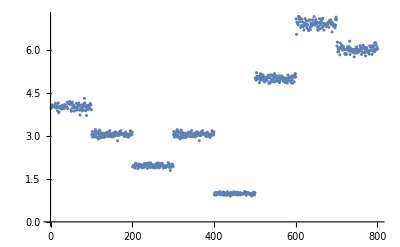

```mathematica
ListPlot[%136]
```

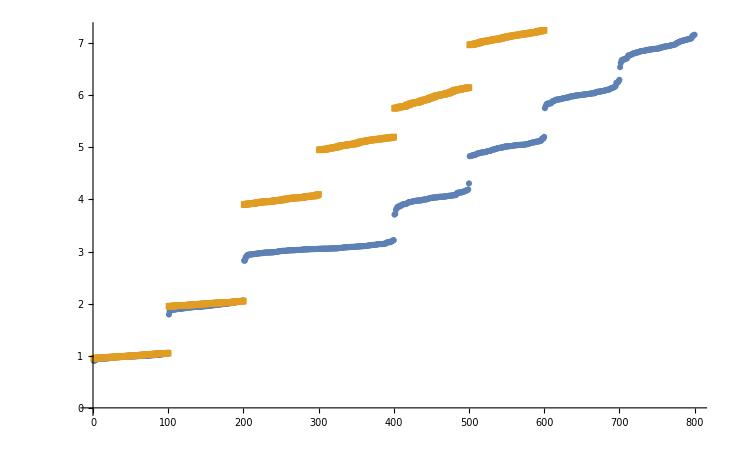

```mathematica
ListPlot[{Sort[%136],Sort[%133]},PlotMarkers->Automatic]
```

```mathematica
Around[%73]
```

4.020.10

```mathematica
Table[intg[0.9,1.5,λ],{λ,100}]
```

{3.92732,4.07809,4.09263,4.15043,4.02552,4.06601,4.01535,4.0805,4.05981,4.03932,4.05405,4.25799,4.03165,3.94567,4.0611,4.10648,3.82073,4.02559,4.22152,3.70082,3.73676,3.94834,3.95519,4.06937,3.9667,4.01772,3.84888,4.08127,3.93627,4.04209,4.06138,4.11695,3.89557,4.02884,4.11292,4.05911,4.07299,4.07013,4.01376,4.01429,4.26169,3.9326,4.26446,4.19826,4.18161,4.32844,4.2092,4.28825,4.1102,3.84677,3.79543,4.22579,4.2776,3.98022,4.12944,3.95872,4.08173,3.75841,3.96009,3.92047,4.02422,3.98869,4.26002,3.90177,3.91009,4.02882,4.12774,4.07606,4.22385,4.05274,3.80255,3.57617,3.81848,3.91911,4.11454,3.98359,4.09299,3.80101,4.00025,4.11359,3.84698,4.21561,4.50852,4.22738,4.02217,3.80818,4.0288,3.54583,3.91689,4.08376,4.05756,3.83609,3.92735,4.03939,4.08218,3.94779,4.23022,4.1472,4.12393,3.88669}

```mathematica
Around[%65]
```

4.030.16

```mathematica
Around[%705]
```

9.000.15

```mathematica
Around[%697]
```

7.970.12

```mathematica
Around[%658]
```

3.990.08

```mathematica
Around[%650]
```

2.990.07

```mathematica
Around[%640]
```

1.420.04

```mathematica
Around[%612]
```

2.180.08

```mathematica
Around[%595]
```

7.010.13

```mathematica
Around[%588]
```

5.930.10

```mathematica
Around[Table[intg[0.9,1.5,λ],{λ,100}]]
```

4.970.10

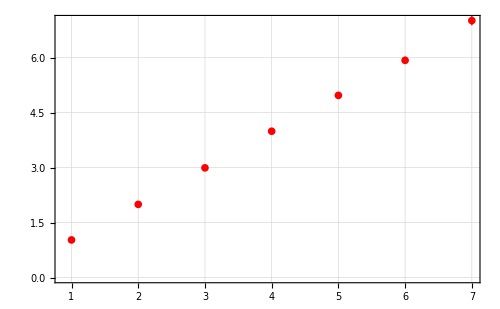

```mathematica
ListPlot[{1.030.04,2.000.08,2.990.07,3.990.08,4.970.10,5.930.10,7.010.13},Frame->True,ImageSize->{500,500},PlotStyle->Red,PlotRange->All,PlotTheme->"Detailed"]
```

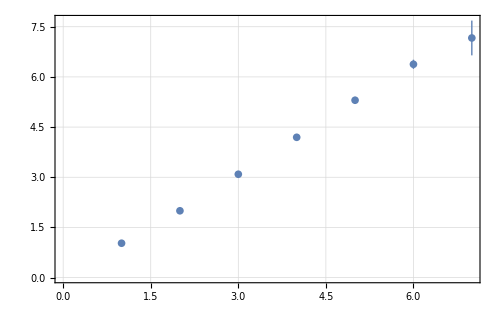

```mathematica
ListPlot[{1.030.04,2.000.08,3.090.08,4.190.09,5.300.10,6.380.14,7.20.5},Frame->True,ImageSize->{500,500},PlotTheme->"Detailed"]
```

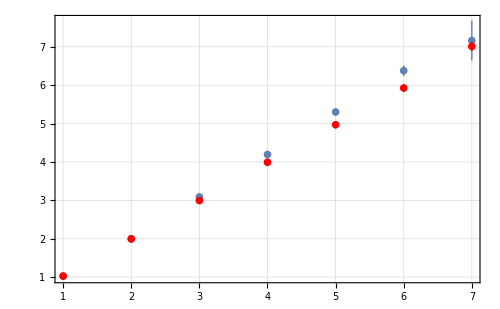

```mathematica
Show[%670,%669,PlotRange->All]
```

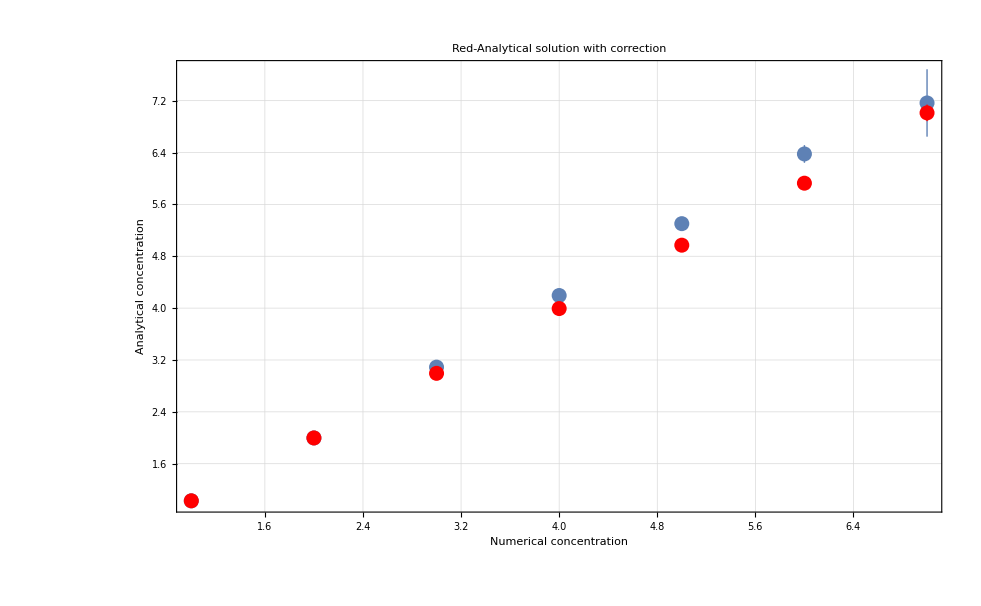

```mathematica
Show[%671,FrameLabel->{{HoldForm[Analytical concentration],None},{HoldForm[Numerical concentration],None}},PlotLabel->HoldForm[Red-Analytical solution with correction],LabelStyle->{16,GrayLevel[0]}]
```

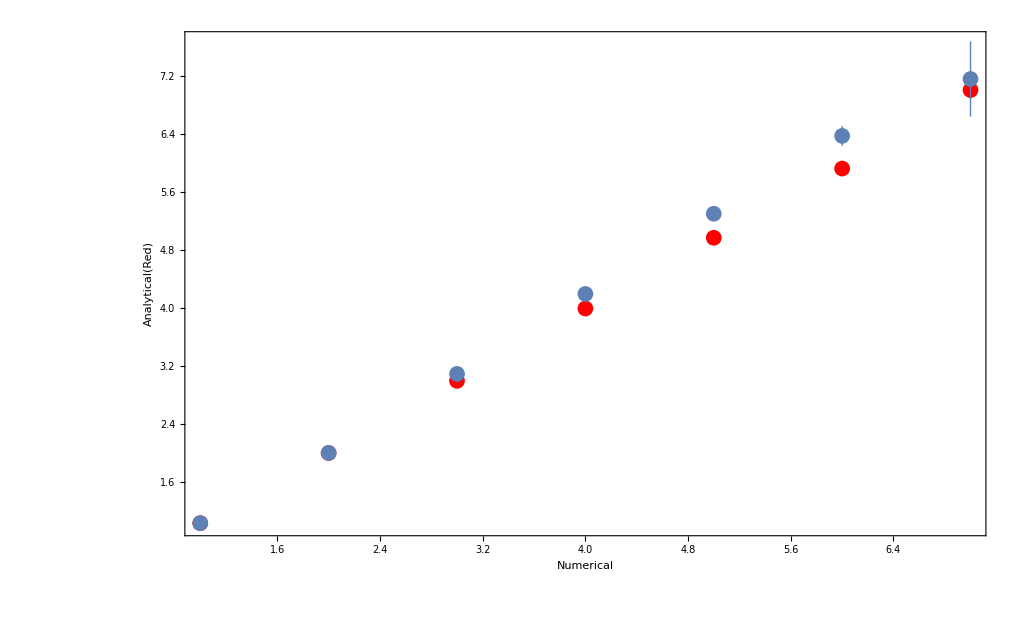

```mathematica
Show[%667,FrameLabel->{{HoldForm[Analytical[Red]],None},{HoldForm[Numerical],None}},PlotLabel->None,LabelStyle->{16,GrayLevel[0]}]
```

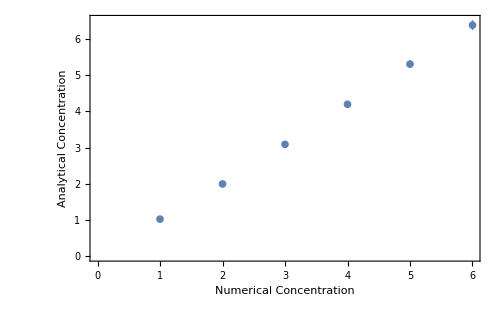

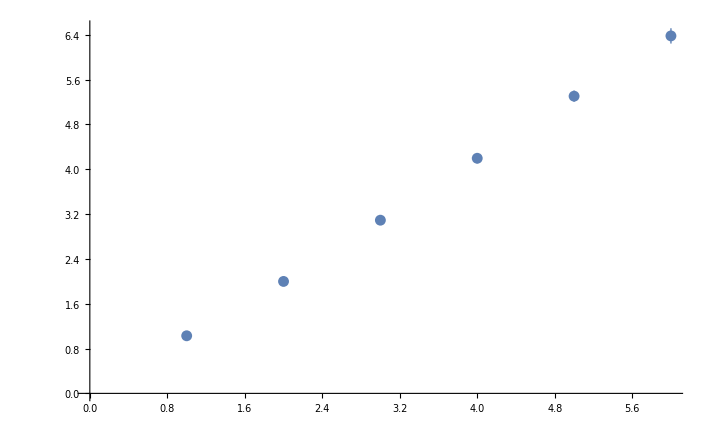

```mathematica
Show[%371,FrameLabel->{{HoldForm[Analytical Concentration],None},{HoldForm[Numerical Concentration],None}},PlotLabel->None,LabelStyle->{16,GrayLevel[0]}]
```